```mathematica
SetDirectory[NotebookDirectory[]];
Trajectories=Import["Trajectories.csv","CSV"];
```

```mathematica
rs={};
For[i=0,i<Length[Trajectories],i++;rs=Append[rs,{Trajectories[[i]][[1]],Trajectories[[i]][[2]]}]]
us={};
For[i=0,i<Length[Trajectories],i++;us=Append[us,{Trajectories[[i]][[1]],Trajectories[[i]][[3]]}]]
rFF={};
For[i=0,i<Length[Trajectories],i++;rFF=Append[rFF,{Trajectories[[i]][[1]],Trajectories[[i]][[4]]}]]
rShell={};
For[i=0,i<Length[Trajectories],i++;rShell=Append[rShell,{Trajectories[[i]][[1]],Trajectories[[i]][[5]]}]]
```

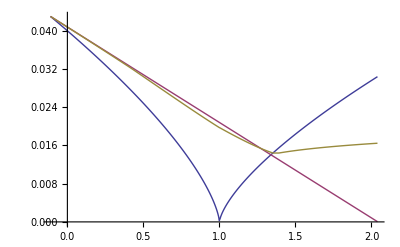

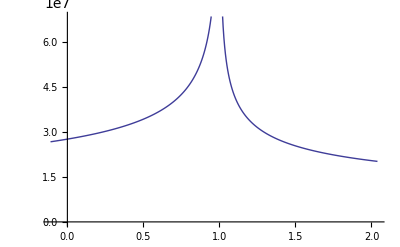

```mathematica
ListLinePlot[{rs,rFF,rShell}]
ListLinePlot[{us}]
```